```mathematica
f[n_,x_,y_]:=Block[{r=Sqrt[x^2+y^2]},b[n,r]((x+ⅈ y)/r)^n]
```

```mathematica
FullSimplify[D[f[n,x,y],x]/.{x->r Cos[θ],y->r Sin[θ]},Assumptions->{r>0,θ∈Reals,n∈Integers}]/.{Cos[θ]->x/r,Sin[θ]->y/r}
```

(ⅇ^(ⅈ n θ) (-(ⅈ n y b[n,r])/r+x b^(0,1)[n,r]))/r

```mathematica
FullSimplify[D[f[n,x,y],y]/.{x->r Cos[θ],y->r Sin[θ]},Assumptions->{r>0,θ∈Reals,n∈Integers}]/.{Cos[θ]->x/r,Sin[θ]->y/r}
```

(ⅇ^(ⅈ n θ) ((ⅈ n x b[n,r])/r+y b^(0,1)[n,r]))/r

```mathematica
f[n_,x_,y_]:=Block[{r=Sqrt[x^2+y^2]},BesselJ[n,r]((x+ⅈ y)/r)^n]
```

```mathematica
FullSimplify[D[f[n,x,y],y]/.{x->r Cos[θ],y->r Sin[θ]},Assumptions->{r∈Reals,θ∈Reals,n∈Integers}]
```

(ⅇ^(ⅈ n θ) (ⅈ ⅇ^(ⅈ θ) n BesselJ[n,r]+r BesselJ[-1+n,r] Sin[θ]))/r

```mathematica
FullSimplify[
(D[f[n,x,y],x]-ⅈ D[f[n,x,y],y])
-f[n-1,x,y]]
```

0

```mathematica
FullSimplify[
(D[f[n,x,y],x]+ⅈ D[f[n,x,y],y])
+f[n+1,x,y]]
```

0

```mathematica
FullSimplify[BesselJ[n+1,r]-(n BesselJ[n,r]/r-D[BesselJ[n,r],r])]
```

0

```mathematica
FullSimplify[BesselJ[n-1,r]-(n BesselJ[n,r]/r+D[BesselJ[n,r],r])]
```

0

```mathematica
FullSimplify[2n BesselJ[n,r]/r-(BesselJ[n-1,r]+BesselJ[n+1,r])]
```

0

```mathematica
FullSimplify[2D[ BesselJ[n,r],r]-(BesselJ[n-1,r]-BesselJ[n+1,r])]
```

0

```mathematica
Animate[
Show[
BarChart[Table[BesselJ[n,x],{n,-5,5}],PlotRange->{-1,1}],Graphics[Line[{{6-1,BesselJ[-1,x]+1},{6+1,BesselJ[1,x]+1}}]]
],
{x,0,5}
]
```

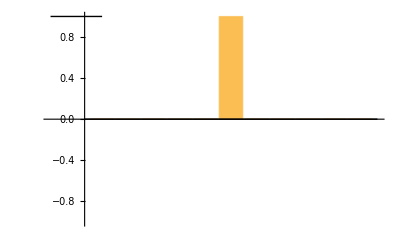

```mathematica
Show[
BarChart[Table[BesselJ[n,0],{n,-5,5}],PlotRange->{-1,1}],Graphics[Line[{{-1,BesselJ[-1,0]+1},{1,BesselJ[1,0]+1}}]]
]
```

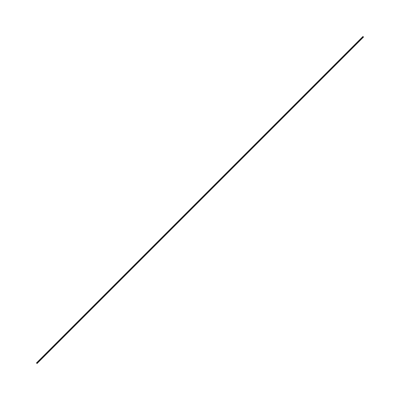

```mathematica
Graphics[{}]
```

```mathematica
a=Animate[
Show[
BarChart[Table[BesselJ[n,x],{n,-5,5}],PlotRange->{-1,1}]
],
{x,0,5}
]
```

```mathematica
a=Table[
Show[
BarChart[Table[BesselJ[n,x],{n,-5,5}],
PlotRange->{-1,1},
ChartLabels->Table[n,{n,-5,5}]
]
],
{x,0,5,0.1}
];
Export["~/Desktop/bessel.gif",a]
```

~/Desktop/bessel.gif

```mathematica
Export["~/Desktop/bessel.gif",a]
```

~/Desktop/bessel.gif

```mathematica
m[n_,x_]:=Table[BesselJ[j-i,x],{i,-n,n},{j,-n,n}]
```

```mathematica
m[5,1.3]//MatrixForm
```

(0.620086 | 0.522023 | 0.183027 | 0.0411358 | 0.00683096 | 0.000900841 | 0.0000985905 | 9.22484×10^-6 | 7.53964×10^-7 | 5.47108×10^-8 | 3.56996×10^-9
-0.522023 | 0.620086 | 0.522023 | 0.183027 | 0.0411358 | 0.00683096 | 0.000900841 | 0.0000985905 | 9.22484×10^-6 | 7.53964×10^-7 | 5.47108×10^-8
0.183027 | -0.522023 | 0.620086 | 0.522023 | 0.183027 | 0.0411358 | 0.00683096 | 0.000900841 | 0.0000985905 | 9.22484×10^-6 | 7.53964×10^-7
-0.0411358 | 0.183027 | -0.522023 | 0.620086 | 0.522023 | 0.183027 | 0.0411358 | 0.00683096 | 0.000900841 | 0.0000985905 | 9.22484×10^-6
0.00683096 | -0.0411358 | 0.183027 | -0.522023 | 0.620086 | 0.522023 | 0.183027 | 0.0411358 | 0.00683096 | 0.000900841 | 0.0000985905
-0.000900841 | 0.00683096 | -0.0411358 | 0.183027 | -0.522023 | 0.620086 | 0.522023 | 0.183027 | 0.0411358 | 0.00683096 | 0.000900841
0.0000985905 | -0.000900841 | 0.00683096 | -0.0411358 | 0.183027 | -0.522023 | 0.620086 | 0.522023 | 0.183027 | 0.0411358 | 0.00683096
-9.22484×10^-6 | 0.0000985905 | -0.000900841 | 0.00683096 | -0.0411358 | 0.183027 | -0.522023 | 0.620086 | 0.522023 | 0.183027 | 0.0411358
7.53964×10^-7 | -9.22484×10^-6 | 0.0000985905 | -0.000900841 | 0.00683096 | -0.0411358 | 0.183027 | -0.522023 | 0.620086 | 0.522023 | 0.183027
-5.47108×10^-8 | 7.53964×10^-7 | -9.22484×10^-6 | 0.0000985905 | -0.000900841 | 0.00683096 | -0.0411358 | 0.183027 | -0.522023 | 0.620086 | 0.522023
3.56996×10^-9 | -5.47108×10^-8 | 7.53964×10^-7 | -9.22484×10^-6 | 0.0000985905 | -0.000900841 | 0.00683096 | -0.0411358 | 0.183027 | -0.522023 | 0.620086)

```mathematica
m[5,0.6].m[5,0.7]//MatrixForm
```

(0.711873 | 0.538578 | 0.184987 | 0.0413089 | 0.00684314 | 0.000901555 | 0.0000986263 | 9.22641×10^-6 | 7.54025×10^-7 | 5.47129×10^-8 | 3.57004×10^-9
-0.536133 | 0.617549 | 0.521723 | 0.183 | 0.041134 | 0.00683085 | 0.000900836 | 0.0000985903 | 9.22483×10^-6 | 7.53963×10^-7 | 5.47113×10^-8
0.184455 | -0.521767 | 0.620116 | 0.522026 | 0.183027 | 0.0411358 | 0.00683096 | 0.000900841 | 0.0000985905 | 9.22484×10^-6 | 7.53981×10^-7
-0.0412437 | 0.183007 | -0.522026 | 0.620086 | 0.522023 | 0.183027 | 0.0411358 | 0.00683096 | 0.000900841 | 0.0000985904 | 9.22537×10^-6
0.00683746 | -0.0411347 | 0.183027 | -0.522023 | 0.620086 | 0.522023 | 0.183027 | 0.0411358 | 0.00683096 | 0.000900839 | 0.0000986045
-0.000901168 | 0.0068309 | -0.0411358 | 0.183027 | -0.522023 | 0.620086 | 0.522023 | 0.183027 | 0.0411358 | 0.0068309 | 0.000901168
0.0000986045 | -0.000900839 | 0.00683096 | -0.0411358 | 0.183027 | -0.522023 | 0.620086 | 0.522023 | 0.183027 | 0.0411347 | 0.00683746
-9.22537×10^-6 | 0.0000985904 | -0.000900841 | 0.00683096 | -0.0411358 | 0.183027 | -0.522023 | 0.620086 | 0.522026 | 0.183007 | 0.0412437
7.53981×10^-7 | -9.22484×10^-6 | 0.0000985905 | -0.000900841 | 0.00683096 | -0.0411358 | 0.183027 | -0.522026 | 0.620116 | 0.521767 | 0.184455
-5.47113×10^-8 | 7.53963×10^-7 | -9.22483×10^-6 | 0.0000985903 | -0.000900836 | 0.00683085 | -0.041134 | 0.183 | -0.521723 | 0.617549 | 0.536133
3.57004×10^-9 | -5.47129×10^-8 | 7.54025×10^-7 | -9.22641×10^-6 | 0.0000986263 | -0.000901555 | 0.00684314 | -0.0413089 | 0.184987 | -0.538578 | 0.711873)